```mathematica
sf=Import["G:\\calc-online\\gpd\\pic\\old\\pic3Dlist-m-n.wdx"];
ft1=Query[1,1]@sf;
ft2=Query[2,1]@sf;
gt1=Query[1,2]@sf;
gt2=Query[2,2]@sf;
fp1=Interpolation[Flatten[ft1,1]];
fp2=Interpolation[Flatten[ft2,1]];
gp1=Interpolation[Flatten[gt1,1]];
gp2=Interpolation[Flatten[gt2,1]];
```

```mathematica
(-2*0.76)^2/(6*2*(0.094)^2*(2Pi)^4)
```

0.0139808

```mathematica
0.5*0.02856607387321113
```

0.014283

```mathematica
rfp1[x_,t_]=0.5*0.02856607387321113*x*fp1[x,t];
rfp2[x_,t_]=0.5*0.02856607387321113*x*fp2[x,t];
rgp1[x_,t_]=0.5*0.02856607387321113*x*gp1[x,t];
rgp2[x_,t_]=0.5*0.02856607387321113*x*gp2[x,t];
```

```mathematica
pf=Show[Plot3D[rfp1[x,t],{x,-0.1,0.1},{t,-1,0}],Plot3D[rfp2[x,t],{x,0.1,1},{t,-1,0}],AxesLabel->{"y","t","yf_(π^+ Δ)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
```

-Graphics3D-

```mathematica
pg=Show[Plot3D[rgp1[x,t],{x,-0.1,0.1},{t,-1,0}],Plot3D[rgp2[x,t],{x,0.1,1},{t,-1,0}],AxesLabel->{"y","t","yg_(π^+ Δ)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
```

-Graphics3D-

```mathematica
pathf=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-m-0.1.pdf"}];
pathg=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-m-0.1.pdf"}];
```

```mathematica
Export[pathf,pf]
Export[pathg,pg]
```

G:\calc-online\gpd\3dre\f-m-0.1.pdf

G:\calc-online\gpd\3dre\g-m-0.1.pdf

```mathematica
rfp11[x_,t_]=0.5*0.02856607387321113*x*fp1[x,-t];
rfp21[x_,t_]=0.5*0.02856607387321113*x*fp2[x,-t];
rgp11[x_,t_]=0.5*0.02856607387321113*x*gp1[x,-t];
rgp21[x_,t_]=0.5*0.02856607387321113*x*gp2[x,-t];
```

```mathematica
pf1=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1}],Plot3D[rfp21[x,t],{x,0.1,1},{t,0.03562509090909091,1}],AxesLabel->{"y","-t(GeV^2)","yf_(π^+ Δ)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
pg1=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.03562509090909091,1},PlotRange->All],Plot3D[rgp21[x,t],{x,0.1,1},{t,0.03562509090909091,1},PlotRange->All],AxesLabel->{"y","-t(GeV^2)","yg_(π^+ Δ)(y)"},LabelStyle->Directive[Thick,Black,12],Frame->True,FrameStyle->Directive[Thick,20]]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathf1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"f-m-fan.pdf"}];
pathg1=FileNameJoin[{"G:\\calc-online\\gpd\\3dre",
"g-m-fan.pdf"}];
```

```mathematica
Export[pathf1,pf1]
Export[pathg1,pg1]
```

G:\calc-online\gpd\3dre\f-m-fan.pdf

G:\calc-online\gpd\3dre\g-m-fan.pdf

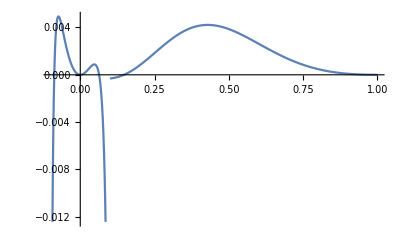

```mathematica
Show[Plot[rfp1[x,-1],{x,-0.1,0.1},PlotRange->{{-0.1,1},Automatic}],Plot[rfp2[x,-1],{x,0.1,1}]]
```

```mathematica
SubsuperscriptBox[yf,"π^+Δ","(rbw)"]//DisplayForm
```

yf_(π^+Δ)^(rbw)

```mathematica
SubsuperscriptBox[yg,"π^+Δ","(rbw)"]//DisplayForm
```

yg_(π^+Δ)^(rbw)

```mathematica
Δ
```

Δ

```mathematica
fn=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],Plot3D[rfp21[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.52,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["yf_(π^+Δ)^(rbw)",Black,35,FontFamily->Times],Scaled[{-0.122,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{-1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
gn=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],Plot3D[rgp21[x,t],{x,0.1,1},{t,0.037,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.52,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["yg_(π^+Δ)^(rbw)",Black,35,FontFamily->Times],Scaled[{-0.1,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{-1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathfn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\new",
"fn-m-front.pdf"}];
pathgn=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\new",
"gn-m-front.pdf"}];
```

```mathematica
Export[pathfn,fn]
Export[pathgn,gn]
```

G:\calc-online\gpd\3dre\24414\new\fn-m-front.pdf

G:\calc-online\gpd\3dre\24414\new\gn-m-front.pdf

```mathematica
gn2=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],Plot3D[rgp21[x,t],{x,0.1,1},{t,0.037,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.52,-0.15,0}]]],Graphics3D[Text[Rotate[Style["-t (GeV^2)",Black,30,FontFamily->Times],60Degree],Scaled[{-0.32,1,0.65}]]],
Graphics3D[Text[Style["yg_(π^+Δ)^(rbw)",Black,35,FontFamily->Times],Scaled[{1.13,-0.2,0.8}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{0,-2,0.8}]
```

-Graphics3D-

```mathematica
pathgn2=FileNameJoin[{"G:\\calc-online\\gpd\\3dre\\24414\\new",
"gn-m-front-2.pdf"}];
Export[pathgn2,gn2]
```

G:\calc-online\gpd\3dre\24414\new\gn-m-front-2.pdf

```mathematica
fn=Show[Plot3D[rfp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],Plot3D[rfp21[x,t],{x,0.1,1},{t,0.037,1},PlotRange->All],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.48,-0.13,0}]]],Graphics3D[Text[Style["-t ",Black,30,FontFamily->Times],Scaled[{-0.16,-0.2,0.8}]]],Graphics3D[Text[Style["(GeV^2)",Black,30,FontFamily->Times],Scaled[{-0.18,-0.3,0.8}]]],
Graphics3D[Text[Style["yf_(π^+Δ)^(rbw)",Black,30,FontFamily->Times],Scaled[{1.64,0.3,0.2}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
gn=Show[Plot3D[rgp11[x,t],{x,-0.1,0.1},{t,0.037,1},PlotRange->All],Plot3D[rgp21[x,t],{x,0.1,1},{t,0.037,1}],
Graphics3D[Text[Style["y",Black,35,FontSlant->Italic,FontFamily->Times],Scaled[{0.48,-0.13,0}]]],Graphics3D[Text[Style["-t ",Black,30,FontFamily->Times],Scaled[{-0.16,-0.2,0.8}]]],Graphics3D[Text[Style["(GeV^2)",Black,30,FontFamily->Times],Scaled[{-0.18,-0.3,0.8}]]],
Graphics3D[Text[Style["yg_(π^+Δ)^(rbw)",Black,30,FontFamily->Times],Scaled[{1.58,0.3,0.2}]]],AxesStyle->Directive[{Black,Thickness[0.003]},12],AxesEdge->{{-1,-1},{-1,-1},{1,-1}},BoxStyle->Directive[{Black,Thickness[0.003]}],TicksStyle->Directive[20,FontFamily->Times],ImageSize->600,ViewPoint->{-0.7,-2,0.8}]
```

-Graphics3D-

-Graphics3D-

```mathematica
pathfn=FileNameJoin[{"G:\\output\\summary\\gpd\\24-4-7-mesonpic",
"fn-m-left.pdf"}];
pathgn=FileNameJoin[{"G:\\output\\summary\\gpd\\24-4-7-mesonpic",
"gn-m-left.pdf"}];
```

```mathematica
Export[pathfn,fn]
Export[pathgn,gn]
```

G:\output\summary\gpd\24-4-7-mesonpic\fn-m-left.pdf

G:\output\summary\gpd\24-4-7-mesonpic\gn-m-left.pdf